1 - 14 Gauss elimination
Solve the linear system given explicitly or by its augmented matrix.

1.  4 x - 6 y = -11
-3 x + 8 y = 10

```mathematica
ClearAll["Global`*"]
```

```mathematica
Solve[4 x- 6y==-11&&-3 x+8 y==10]
```

{{x→-2,y→1/2}}

The green cell above agrees with the text answer.

3.  x + y - z = 9, 8 y + 6 z = -6, -2 x + 4 y - 6 z = 40

```mathematica
ClearAll["Global`*"]
```

```mathematica
Solve[x+y-z==9&&8 y+6 z==-6&&-2 x+4 y-6z==40]
```

{{x→1,y→3,z→-5}}

The green cell above agrees with the text answer.

5. (13 | 12 | -6
-4 | 7 | -73
11 | -13 | 157)

{{65.,60.,-30.},{-20.,35.,-365.},{55.,-65.,785.}}

```mathematica
ClearAll["Global`*"]
```

```mathematica
Solve[13 x+12 y+-6 z==0&&-4 x+7 y-73 z==0&&11 x-13 y+157 z==0,{x,y}]
```

{{x→-6 z,y→7 z}}

```mathematica
A=({{13, 12, -6}, {-4, 7, -73}, {11, -13, 157}})
```

{{13,12,-6},{-4,7,-73},{11,-13,157}}

```mathematica
RowReduce[A]
```

```mathematica
{{1,0,6},{0,1,-7},{0,0,0}}
```

Above: It is seen from inspection that x=6 and y=-7, the same values found in the text.

7. (2 | 4 | 1 | 0
-1 | 1 | -2 | 0
4 | 0 | 6 | 0)

{{14.,28.,7.,0.},{-7.,7.,-14.,0.},{28.,0.,42.,0.}}

```mathematica
ClearAll["Global`*"]
```

```mathematica
A=({{2, 4, 1, 0}, {-1, 1, -2, 0}, {4, 0, 6, 0}})
```

{{2,4,1,0},{-1,1,-2,0},{4,0,6,0}}

```mathematica
e1=RowReduce[A]//MatrixForm
```

(1 | 0 | 3/2 | 0
0 | 1 | -1/2 | 0
0 | 0 | 0 | 0)

```mathematica
Solve[x+3/2 z==0&&y-1/2 z==0,{x,z}]
```

{{x→-3 y,z→2 y}}

Above: The text sets y=t, but this is not necessary.  Either one is arbitrary in value. To accord with text, x=-3 t, z=2 t.

9. (0 | -2 | -2 | -8
3 | 4 | -5 | 13)

{{0.,-18.,-18.,-72.},{27.,36.,-45.,117.}}

```mathematica
ClearAll["Global`*"]
```

```mathematica
Solve[-2 y-2 z==-8&&3 x+4 y-5 z==13,{x,y}]
```

{{x→-1+3 z,y→4-z}}

Above: The answer agrees with text, provided a parameter t is invented such that z=t.

11. (0 | 5 | 5 | -10 | 0
2 | -3 | -3 | 6 | 2
4 | 1 | 1 | -2 | 4)

{{0.,55.,55.,-110.,0.},{22.,-33.,-33.,66.,22.},{44.,11.,11.,-22.,44.}}

```mathematica
Clear["Global`*"]
```

```mathematica
A=({{0, 5, 5, -10, 0}, {2, -3, -3, 6, 2}, {4, 1, 1, -2, 4}})
```

{{0,5,5,-10,0},{2,-3,-3,6,2},{4,1,1,-2,4}}

Below: The row reduction comes up with a null row. Is that an ominous sign?

```mathematica
e1=RowReduce[A]
```

{{1,0,0,0,1},{0,1,1,-2,0},{0,0,0,0,0}}

The dot product has fewer equation seeds than there are rows in the A matrix. I play around with the assigned positions and signs of t1 and t2 to try to come up with the text answer.

```mathematica
e2=e1.{x,y,z,t2,-t1}
```

{-t1+x,-2 t2+y+z,0}

```mathematica
Solve[-t1+x==0&&-2t2+y+z==0,{x,y}]
```

{{x→t1,y→2 t2-z}}

Let me trot out the text answer: x = t_1 arb.; y = 2 t_2 - t_1; z = t_2 arb. Rearranging the text answer results in the equation y = 2z - x. If I adopt the stance that z = t_2, then I can make the same equation out of the results above, that is, y = 2z - x.

13. (0 | 10 | 4 | -2 | -4
-3 | -17 | 1 | 2 | 2
1 | 1 | 1 | 0 | 6
8 | -34 | 16 | -10 | 4)

{{0.,130.,52.,-26.,-52.},{-39.,-221.,13.,26.,26.},{13.,13.,13.,0.,78.},{104.,-442.,208.,-130.,52.}}

```mathematica
ClearAll["Global`*"]
```

```mathematica
e1=({{0, 10, 4, -2, -4}, {-3, -17, 1, 2, 2}, {1, 1, 1, 0, 6}, {8, -34, 16, -10, 4}})
```

{{0,10,4,-2,-4},{-3,-17,1,2,2},{1,1,1,0,6},{8,-34,16,-10,4}}

```mathematica
e2=RowReduce[e1]
```

{{1,0,0,0,4},{0,1,0,0,0},{0,0,1,0,2},{0,0,0,1,6}}

```mathematica
e3=e2.{w,x,y,z,t1}
```

{4 t1+w,x,2 t1+y,6 t1+z}

```mathematica
e4=Solve[4 t1+w==0&&2 t1+y==0&&6 t1+z==0&&x==0]
```

{{w→-4 t1,x→0,y→-2 t1,z→-6 t1}}

```mathematica
e5=e4/.t1->-1
```

{{w→4,x→0,y→2,z→6}}

Above: The answer matches the text.

17 - 21 Models of networks
In problems 17 - 19, using Kirchhoff’s laws (see example 2) and showing details, find the currents:

17. As shown in diagram below.

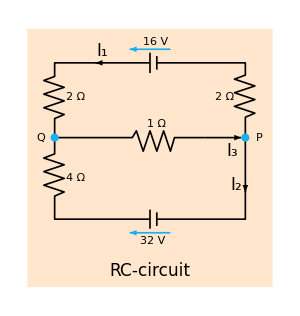

```mathematica
Graphics[{{LightOrange,Rectangle[{1.1,0.2},{2.9,2.1}]},(*{LightGray,Table[{Line[{{1,n},{3,n}}]},{n,0,2.2,0.1}]},{LightGray,Table[{Line[{{n,0},{n,2.2}}]},{n,1,3,0.1}]},*){Thickness[0.004],Line[{{1.3,1.3},{1.3,1.18},{1.22,1.15},{1.37,1.1},{1.22,1.05},{1.37,1},{1.22,0.95},{1.37,0.9},{1.3,0.87},{1.3,0.7},{2,0.7}}]},{Thickness[0.004],Line[{{2.05,0.7},{2.7,0.7},{2.7,0.95}}]},{Thickness[0.004],Line[{{2.7,1.3},{2.7,1.45},{2.77,1.48},{2.62,1.53},{2.77,1.58},{2.62,1.63},{2.77,1.68},{2.62,1.73},{2.7,1.76},{2.7,1.85},{2.05,1.85}}]},{Thickness[0.004],Line[{{1.65,1.85},{1.3,1.85},{1.3,1.75},{1.22,1.72},{1.37,1.67},{1.22,1.62},{1.37,1.57},{1.22,1.52},{1.37,1.47},{1.3,1.44},{1.3,1.3}}]},
{Thickness[0.004],Arrow[{{2,1.85},{1.6,1.85}}]},{Thickness[0.004],Arrow[{{2.7,1.3},{2.7,0.9}}]},{Thickness[0.004],Arrow[{{2.4,1.3},{2.67,1.3}}]},{Text[Style["1 Ω",Medium],{2.05,1.4}]},{Text[Style["2 Ω",Medium],{2.55,1.6}]},{Text[Style["2 Ω",Medium],{1.45,1.6}]},{Text[Style["4 Ω",Medium],{1.45,1}]},{Text[Style["32 V",Medium],{2.02,0.54}]},{Text[Style["RC-circuit",17],{2,0.32}]},{Text[Style["16 V",Medium],{2.04,2}]},{Thickness[0.004],Line[{{1.3,1.3},{1.87,1.3},{1.9,1.35},{1.95,1.2},{2,1.35},{2.05,1.2},{2.1,1.35},{2.15,1.2},{2.18,1.3},{2.4,1.3}}]},{Thickness[0.004],Line[{{2,1.775},{2,1.925}}]},{Thickness[0.004],Line[{{2,0.63},{2,0.77}}]},{Thickness[0.004],Line[{{2.05,1.8},{2.05,1.9}}]},{Thickness[0.004],Line[{{2.05,0.65},{2.05,0.75}}]},{Thickness[0.004],RGBColor[0.113,0.686,0.925],Arrow[{{2.15,1.95},{1.85,1.95}}]},{Thickness[0.004],RGBColor[0.113,0.686,0.925],Arrow[{{2.15,0.6},{1.85,0.6}}]},{RGBColor[0.113,0.686,0.925],Disk[{1.3,1.3},0.03]},{RGBColor[0.113,0.686,0.925],Disk[{2.7,1.3},0.03]},{Text[Style["I_1",17],{1.65,1.94}]},{Text[Style["I_2",17],{2.63,0.95}]},{Text[Style["I_3",17],{2.6,1.2}]},{Text[Style["Q",Medium],{1.2,1.3}]},{Text[Style["P",Medium],{2.8,1.3}]},{Thickness[0.004],Circle[{1.76,0.7},0.1,{-0.85,π}]},{Thickness[0.004],Circle[{1.89,0.7},0.1,{-0.85,π+0.85}]},{Thickness[0.004],Circle[{2.02,0.7},0.1,{-0.85,π+0.85}]},{Thickness[0.004],Circle[{2.15,0.7},0.1,{0,π+0.85}]}},Axes->False,ImageSize->300(*,Ticks->{Range[0,3,0.1],Range[0,2.2,0.1]}*)]
```

Considering only node P, and trying to put the Wikipedia information into effect, I have the equation I_3-I_2-I_1=0 (Kirchhoff’s current law, which is strictly relative to P, not a clock) plus the two equations -(1)*I_3-2*I_1-16-2 I_1=0 and I_3+32+4 I_2=0 (Kirchhoff’s voltage law, in which each loop is considered with clockwise considered as positive).

```mathematica
Clear["Global`*"]
```

```mathematica
Solve[Subscript[iI, 3]-Subscript[iI, 2]-Subscript[iI, 1]==0&&-(1)*Subscript[iI, 3]-2*Subscript[iI, 1]-16-2 Subscript[iI, 1]==0&&Subscript[iI, 3]+32+4 Subscript[iI, 2]==0,{Subscript[iI, 1],Subscript[iI, 2],Subscript[iI, 3]}]
```

{{iI_1→-2,iI_2→-6,iI_3→-8}}

The above green cell matches the text answer, the signs of current being uniformly opposite to the text answer merely informing me that all assumptions about current direction should be reversed. I can also get a solution to the steady state current online, at https://falstad.com/circuit/. The online version is live, and by double-clicking the three branches, the correct current for each branch is revealed. Thus I have two separate ways, other than state space, to track down the steady state current.

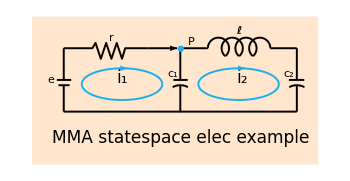

```mathematica
Graphics[{{LightOrange,Rectangle[{1.3,0.2},{4,1.6}]},(*{LightGray,Table[{Line[{{1,n},{4,n}}]},{n,0,2.2,0.1}]},{LightGray,Table[{Line[{{n,0},{n,2.2}}]},{n,1,4,0.1}]},*){Thickness[0.004],Line[{{2.0,0.7},{2.7,0.7},{2.7,0.95}}]},
{Thickness[0.004],Arrow[{{2.4,1.3},{2.67,1.3}}]},{Text[Style["r",Medium],{2.05,1.4}]},{Text[Style["e",Medium],{1.48,1}]},{Text[Style["c_2",Medium],{3.72,1.06}]},{Text[Style["MMA statespace elec example",17],{2.7,0.45}]},{Text[Style["ℓ",Medium,Bold],{3.25,1.46}]},{Thickness[0.004],Line[{{1.6,1.3},{1.87,1.3},{1.9,1.35},{1.95,1.2},{2,1.35},{2.05,1.2},{2.1,1.35},{2.15,1.2},{2.18,1.3},{2.4,1.3}}]},{Text[Style["i_1",17],{2.15,1.02}]},{Text[Style["c_1",Medium],{2.63,1.06}]},{Text[Style["i_2",17],{3.28,1.02}]},{Text[Style["P",Medium],{2.8,1.36}]},{Thickness[0.004],Line[{{2.7,0.7},{3.8,0.7}}]},{Thickness[0.004],Line[{{2.7,1.3},{2.96,1.3}}]},{Thickness[0.004],Line[{{3.55,1.3},{3.8,1.3}}]},{Thickness[0.004],Line[{{3.8,1.3},{3.8,1.0}}]},{Thickness[0.004],Line[{{3.8,0.95},{3.8,0.7}}]},{Thickness[0.004],Circle[{3.06,1.3},0.1,{-0.85,π}]},{Thickness[0.004],Circle[{3.19,1.3},0.1,{-0.85,π+0.85}]},{Thickness[0.004],Circle[{3.32,1.3},0.1,{-0.85,π+0.85}]},{Thickness[0.004],Circle[{3.45,1.3},0.1,{0,π+0.85}]},{Thickness[0.004],Line[{{3.725,1},{3.87,1}}]},{Thickness[0.004],Circle[{2.7,0.8},0.15,{π/2-0.5,π/2+0.5}]},{Thickness[0.004],Circle[{3.8,0.8},0.15,{π/2-0.5,π/2+0.5}]},{Thickness[0.004],Line[{{2.7,1.3},{2.7,1.0}}]},{Thickness[0.004],Line[{{2.635,1},{2.77,1}}]},{Thickness[0.004],Line[{{1.6,1.3},{1.6,1}}]},{Thickness[0.004],Line[{{1.6,0.95},{1.6,0.7}}]},{Thickness[0.004],Line[{{1.535,1},{1.67,1}}]},{Thickness[0.004],Line[{{1.55,0.95},{1.655,0.95}}]},{Thickness[0.004],Line[{{1.6,0.7},{2,0.7}}]},{RGBColor[0.113,0.686,0.925],Disk[{2.7,1.3},0.03]},{RGBColor[0.113,0.686,0.925],Thickness[0.004],Circle[{2.15,0.96},{0.38,0.15},{0,2π}]},{RGBColor[0.113,0.686,0.925],Arrowheads[0.03],Arrow[BezierCurve[{{2.15,1.11},{2.2,1.11}}]]},{RGBColor[0.113,0.686,0.925],Thickness[0.004],Circle[{3.25,0.96},{0.38,0.15},{0,2π}]},{RGBColor[0.113,0.686,0.925],Arrowheads[0.03],Arrow[BezierCurve[{{3.28,1.11},{3.31,1.11}}]]}},Axes->False,ImageSize->350(*,Ticks->{Range[0,3,0.1],Range[0,2.2,0.1]}*)]
```

Not this exact problem, but I could look at the Mathematica documentation example for a two-loop circuit. The sketch is shown above.

Component relations are entered, and state conditions are recorded.

```mathematica
components={L Subscript[i, 2]'[t]==Subscript[v, l][t],Subscript[v, c1]'[t]==(Subscript[i, 1][t])/Subscript[C, 1],Subscript[v, c2]'[t]==(Subscript[i, 2][t])/Subscript[C, 2]};kirchhoff={R (Subscript[i, 1][t]+Subscript[i, 2][t])==Subscript[v, r][t],Subscript[v, c1][t]+Subscript[v, r][t]==Subscript[v, s][t],Subscript[v, c1][t]==Subscript[v, l][t]+Subscript[v, c2][t]};
```

Then the state space model is created.

```mathematica
m1=StateSpaceModel[Join[components,kirchhoff],{ Subscript[v, c1][t], Subscript[v, c2][t], Subscript[i, 2][t],Subscript[i, 1][t],Subscript[v, r][t], Subscript[v, l][t]}, Subscript[v, s][t], Subscript[v, c2][t],t]
```

00-L00000000-10-100000000-1/C_10000-1000000-1/C_2000000000000RR-100000000100010-10000001-1000-100100000StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4$CellContext`stname5$CellContext`stname6Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1161FalseFalseTrueAutomaticNone,{{i_2[t],0},{v_c1[t],0},{v_l[t],0},{i_1[t],0},{v_r[t],0},{v_c2[t],0}},{{v_s[t],0}},Automatic,t

At this point specific values for the components can be set or reset.

```mathematica
mw=m1/.{Subscript[C, 1]->2,Subscript[C, 2]->3,L->1,R->2}
```

00-100000000-10-100000000-1/20000-1000000-1/300000000000022-100000000100010-10000001-1000-100100000StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4$CellContext`stname5$CellContext`stname6Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1161FalseFalseTrueAutomaticNone,{{i_2[t],0},{v_c1[t],0},{v_l[t],0},{i_1[t],0},{v_r[t],0},{v_c2[t],0}},{{v_s[t],0}},Automatic,t

And finally the voltage is plugged in and the time-varying behavior is observed. I don’t like the output response to this model, I would like to see multiple traces for the multiple loops (of the circuit).

```mathematica
opc=OutputResponse[{mw},12,{t,0,60}]
```

{InterpolatingFunction[{{0., 60.}}, <>][t]}

From the plot below, I seem to be seeing a gradual stabilization to the 12 volts entered as the ‘e’ value. However, I would expect to be seeing current, not potential.

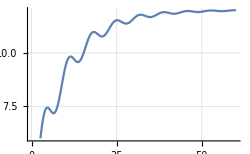

```mathematica
Plot[opc, {t,0,60},ImageSize->250,GridLines->Automatic]
```

If state responses are considered, I see that there is a different one for each second. These are sinusoidal, but I don’t know why the 5th is nearly flat, but the 4th and 6th are pretty curvy.

```mathematica
ops=StateResponse[{mw},12,{t,0,6}];
```

```mathematica
p1=Plot[ops[[1]],{t,0,5},PlotStyle->Red,PlotRange->{{0,5},{-5,10}}];
p2=Plot[ops[[2]],{t,0,5},PlotStyle->Blue];
p3=Plot[ops[[3]],{t,0,5},PlotStyle->Green];
p4=Plot[ops[[4]],{t,0,5},PlotStyle->Orange];
p5=Plot[ops[[5]],{t,0,5},PlotStyle->Pink];
p6=Plot[ops[[6]],{t,0,5},PlotStyle->Black];
```

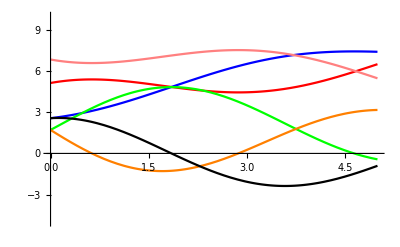

```mathematica
Show[p1,p2,p3,p4,p5,p6]
```